## 134Ce - Petrache study

## The wobbling bands [9,7]

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
band9En=Sort[N[#/1000]&@{8583,7581,6597,5724,4907,4183,3719}];
band9Spins=Table[i,{i,10,22,2}];
band7En=Sort[N[#/1000]&@{5717,4924,4384}];
band7Spins=Table[i,{i,11,15,2}];
```

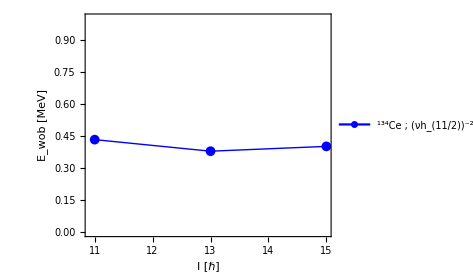

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Ce-Nucleus/134Ce-2.pdf";
wobbling[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i]]+yrast[[i+1]])},{i,1,Length[onephonon]}];
data=wobbling[band9En,band7En,band7Spins];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{Style[Row[{Superscript["","134"],"Ce ; (νh_(11/2))^-2"}],FontFamily->"Times",30]},{0.5,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export[m1minipath,fig];
Show[fig]
```